## Problem Specification

Consider a state x, where
x1 = distance to the car in front
x2 = velocity of following car
and the safety constraint is x1 ≥ 2 x2

a linear drag model is used, for simplicity
and the maximum acceleration and deceleration are 0.25 gs.

```mathematica
x = {x1, x2};

(*Params*)
m = 1650.0;
f0 = 0.1;
f1 =5.0;
f2 = 0.25 ;
v0 =13.89;
vmax = 24.0;

(*Dynamics:*)
f = {v0 - x2, -(f0 + f1 x2 + f2 x2^2)/m};
g = {0, 9.81};

(*Safety:*)
h = x1 -1.8x2;

(*Input Constraints:*)
umax =0.25;
myAbs[x_]:= If[x≥ 0, x, -x];
```

## Construct ICCBFs:

```mathematica
b0 = h//FullSimplify
Lfb0 = Grad[b0, x].f//FullSimplify
Lgb0 = Grad[b0, x].g//FullSimplify

b0dotinf= Lfb0 - myAbs[Lgb0] * umax//FullSimplify
b0dotsup= Lfb0 + myAbs[Lgb0] * umax//FullSimplify
```

x1-1.8 x2

13.8901+(-0.994545+0.000272727 x2) x2

-17.658

9.47561+(-0.994545+0.000272727 x2) x2

18.3046+(-0.994545+0.000272727 x2) x2

Thus, the safe region can be plotted.

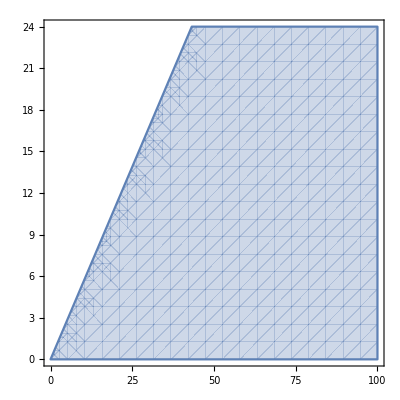

```mathematica
safereg = RegionPlot[b0≥ 0, {x1, 0, 100},{x2, 0, vmax}]
```

We can verify if h is a CBF, by plotting the region where sup(\dot h) \geq 0:

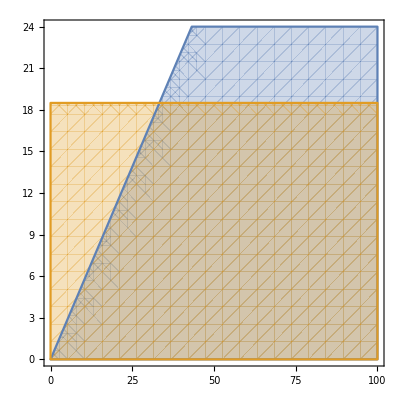

```mathematica
RegionPlot[{b0≥ 0,b0dotsup ≥ 0}, {x1, 0, 100},{x2, 0, vmax}]
```

and therefore, if the speed of the car is above ~17 m/s, on the boundary of the safe set, the car cannot decelerate fast enough to stay safe. 
As such, we introduce a new function b1:

```mathematica
k0 = 4
b1 = b0dotinf + k0 *b0

Lfb1 = Grad[b1, x].f//FullSimplify
Lgb1 = Grad[b1, x].g//FullSimplify

b1dotinf= Lfb1 - myAbs[Lgb1] * umax//FullSimplify
b1dotsup= Lfb1 + myAbs[Lgb1] * umax//FullSimplify
```

4

9.47561+4 (x1-1.8 x2)+(-0.994545+0.000272727 x2) x2

55.5605+x2 (-3.97517+(0.00123994-8.26446×10^-8 x2) x2)

-80.3885+0.00535091 x2

Piecewise[{{35.4634+x2 (-3.97383+(0.00123994-8.26446×10^-8 x2) x2), x2<15023.3}, {75.6576+x2 (-3.97651+(0.00123994-8.26446×10^-8 x2) x2), True}}]

Piecewise[{{35.4634+x2 (-3.97383+(0.00123994-8.26446×10^-8 x2) x2), x2≥15023.3}, {75.6576+x2 (-3.97651+(0.00123994-8.26446×10^-8 x2) x2), True}}]

Now we can plot regions where b1 >= 0

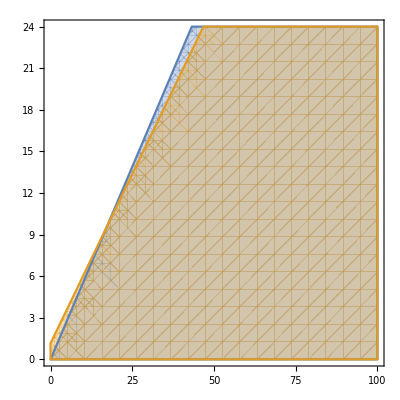

```mathematica
C1plot = RegionPlot[{b0≥ 0, b1≥0 }, {x1, 0, 100},{x2, 0, vmax}]
```

Which shows a shallower gradient - b1 has restricted the safe set to a smaller set. 
Lets verify if b1 can be forward invariant, by plotting sup(b1 dot):

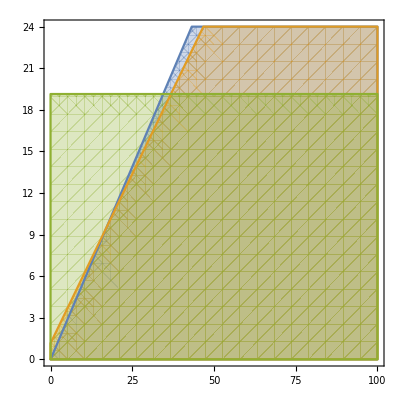

```mathematica
RegionPlot[{b0≥ 0, b1≥0 , b1dotsup≥ 0}, {x1, 0, 100},{x2, 0, vmax}]
```

Thus, no, it cannot be rendered safe, for any x_2 > ~ 20 m/s. Lets try again,

```mathematica
k1=7
b2 = b1dotinf + k1 *Sqrt[ b1]

Lfb2 = Grad[b2, x].f//Simplify;
Lgb2 = Grad[b2, x].g//Simplify;

b2dotinf= Lfb2 - myAbs[Lgb2] * umax//Simplify;
b2dotsup= Lfb2 + myAbs[Lgb2] * umax//Simplify;
```

7

7 √(9.47561+4 (x1-1.8 x2)+(-0.994545+0.000272727 x2) x2)+(Piecewise[{{35.4634+x2 (-3.97383+(0.00123994-8.26446×10^-8 x2) x2), x2<15023.3}, {75.6576+x2 (-3.97651+(0.00123994-8.26446×10^-8 x2) x2), True}}])

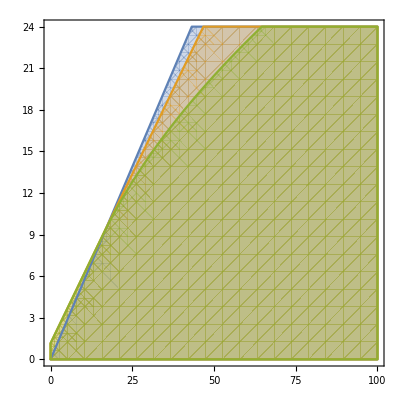

GreaterEqual::nord: Invalid comparison with 22.9268+16.9638 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -38.9065+116.077 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 12.9153+16.4405 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

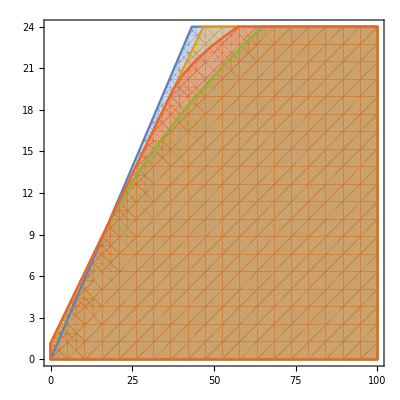

```mathematica
C2plot = RegionPlot[{b0≥ 0, b1≥0 , b2≥ 0}, {x1, 0, 100},{x2, 0, vmax}]
RegionPlot[{b0≥ 0, b1≥0 , b2≥ 0, b2dotsup≥ 0}, {x1, 0, 100},{x2, 0, vmax}]
```

Thus, the safe set and inner safe set can be plotted:

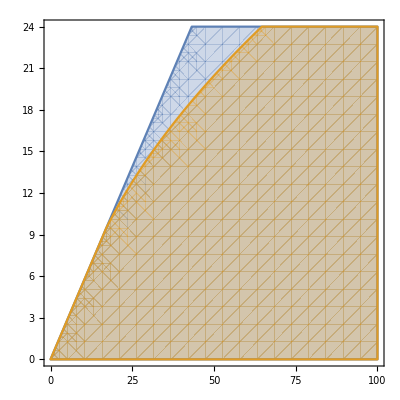

```mathematica
regs = RegionPlot[{b0≥ 0, b0≥ 0 && b1≥0  &&  b2≥ 0 && 0≤ x2 ≤ vmax}, {x1, 0, 100},{x2, 0, vmax}]
```

## Verification of ICCBF

Now we verify if we have found an ICCBF:

```mathematica
k2 =2;
fun = b2dotsup + k2 b2//Simplify;
(*and fun must be positive for all x in the domain of interest*)
Xdom =( 0≤ x1) && (0≤ x2≤ vmax);
CstarSet = b0 ≥ 0 && b1≥ 0 && b2≥ 0;
domain =  Xdom&& CstarSet//Simplify;
```

```mathematica
Minimize[{fun,domain},{x1,x2}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.33419,{x1→64.6367,x2→24.}}

Which is positive. 
Therefore we have found an ICCBF.

We can be a bit more careful, and check local optimization results over a grid, with step size of 10 and 6 in the  x1 and x2 directions respectively.

```mathematica
For[x10 = 0, x10≤ 100,x10=x10+10,
For[x20 = 0, x20≤ vmax, x20=x20+6,
If[domain/.{x1-> x10, x2-> x20} , (*if initial point is in the domain*)
Print[FindMinimum[{fun,domain},{{x1,x10},{x2,x20}}]]
]
]
]
```

{2.33589,{x1→64.6372,x2→24.}}

{2.33589,{x1→64.6372,x2→24.}}

{2.33589,{x1→64.6372,x2→24.}}

«35 more identical outputs»

And therefore all the local solutions point to the same minimum.

```mathematica
b0/.{x1->64.6371896885372,x2->24.}
b1/.{x1->64.6371896885372,x2->24.}
b2/.{x1->64.6371896885372,x2->24.}
```

21.4372

71.5124

1.19949×10^-6

The minimum is achieved at the boundary of b2.

## QP-based Control Design

Now finally, we can define a controller using ICCBFs.
we will always find a u such that 
b2dot >= -alpha b2
and also constrain it to lie inside U.

Therefore, we define the controller:

```mathematica
V = (x2- vmax)^2;
LfV = Grad[V,x].f//FullSimplify;
LgV = Grad[V,x].g//FullSimplify;
ud =  (u/.(Solve[LfV + LgV u ==  -10 V, u]//Simplify))[[1]]
```

(-293.578+24.4574 x2-0.509746 x2^2+0.000015445 x2^3)/(-24.+x2)

We define both the ICCBF-QP [this work], and the CBF-CLF-QP from [Ames 2014]

```mathematica
controllerICCBFQP = ArgMin[{(u-ud)^2, -umax ≤  u ≤  umax && Lfb2 + Lgb2 u ≥ -k2 b2} ,u];
controllerCLFCBFQP = Clip[{1,0}.ArgMin[{u^2+ (10^(-1))δ,(LfV + LgV u ≤ -10 V + δ) && (Lfb0 + Lgb0 u ≥ -k2 b0) &&( δ ≥ 0)} ,{u, δ}],{-umax, umax}]
(*controllerCLFCBFQP = ArgMin[{(u-ud)^2, Lfb0 + Lgb0 u ≥ -k2 b0} ,u];*)
```

Clip[{1,0}.ArgMin[{u^2+δ/10,0.00290909+19.62 u (-24.+x2)+x2 (0.145333+(0.00121212-0.00030303 x2) x2)≤-10 (-24.+x2)^2+δ&&13.8901-17.658 u+(-0.994545+0.000272727 x2) x2≥-2 (x1-1.8 x2)&&δ≥0},{u,δ}],{-0.25,0.25}]

Test:

```mathematica
controllerICCBFQP/.{x1-> 60, x2-> 22}
```

0.0171714

```mathematica
controllerCLFCBFQP/.{x1-> 60, x2-> 22}
```

0.25

## Closed-loop Simulations

Define the closed loop dynamics:

```mathematica
fclICCBFQP = f + g * controllerICCBFQP//Simplify;
fclCLFCBFQP = f + g * controllerCLFCBFQP//Simplify;
```

```mathematica
fclICCBFQP1= fclICCBFQP[[1]]/.{x1-> y1[t], x2-> y2[t]};
fclICCBFQP2 = fclICCBFQP[[2]]/.{x1-> y1[t], x2-> y2[t]};

fclCLFCBFQP1 = fclCLFCBFQP[[1]]/.{x1-> y1[t], x2-> y2[t]};
fclCLFCBFQP2 = fclCLFCBFQP[[2]]/.{x1-> y1[t], x2-> y2[t]};
```

Define the initial condition:

```mathematica
initial = {100, 20} ;
```

Construct the equations for NDSolve:

```mathematica
eqnsICCBFQP = {y1'[t]== fclICCBFQP1, y2'[t] == fclICCBFQP2,  y1[0] == initial[[1]], y2[0] == initial[[2]]};
eqnsCLFCBFQP = {y1'[t]== fclCLFCBFQP1, y2'[t] == fclCLFCBFQP2, y1[0] == initial[[1]], y2[0] == initial[[2]]};
```

Solve:

```mathematica
tmax = 20;
solICCBFQP = NDSolve[eqnsICCBFQP, {y1, y2},{t, 0, tmax}]
solCLFCBFQP= NDSolve[eqnsCLFCBFQP, {y1, y2},{t, 0, tmax}]
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

Extract the domain where a solution was found:

```mathematica
domICCBFQP = (y1/.solICCBFQP)[[1]][[1]][[1]][[2]] (*Stores the domain of the solution*)
domCLFCBFQP= (y1/.solCLFCBFQP)[[1]][[1]][[1]][[2]] (*Stores the domain of the solution*)
```

20.

20.

Solution Plots:

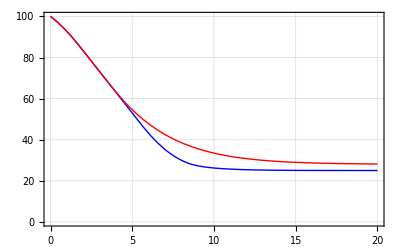

```mathematica
(*Plot of dist between cars vs time*)
Plot[{
If[t≤ domCLFCBFQP, Evaluate[y1[t]/.solCLFCBFQP], Indeterminate],
If[t≤ domICCBFQP, Evaluate[y1[t]/.solICCBFQP], Indeterminate]
}, {t, 0, tmax}, 
PlotRange->Full, AxesOrigin->{0,0}, Frame->True, GridLines->Automatic, PlotStyle->{{Thick, Blue}, {Thick, Red}}]
```

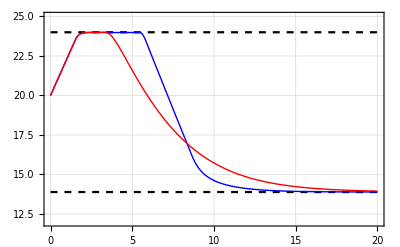

```mathematica
(*Plot of speed of car vs time*)
Plot[{vmax,v0, 
 If[t≤ domCLFCBFQP, Evaluate[y2[t]/.solCLFCBFQP], Indeterminate],
If[t≤ domICCBFQP, Evaluate[y2[t]/.solICCBFQP], Indeterminate]
}, {t, 0, tmax},
 PlotRange->{12, 25}, AxesOrigin->{0,0}, Frame->True, GridLines->Automatic, PlotStyle->{{Dashed,Black} ,{Dashed,Black} ,{Thick, Blue}, {Thick, Red}}]
```

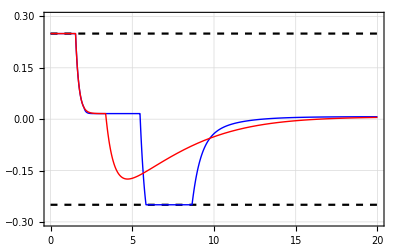

```mathematica
(*Plot of control history vs time*)
uICCBFQP = (controllerICCBFQP/.{x1-> y1[t], x2-> y2[t]})/.solICCBFQP;
uCLFCBFQP = (controllerCLFCBFQP/.{x1-> y1[t], x2-> y2[t]})/.solCLFCBFQP;
Plot[{ umax, -umax, 
If[t≤ domCLFCBFQP,uCLFCBFQP,Indeterminate],
If[t≤ domICCBFQP, uICCBFQP, Indeterminate]},
 {t, 0, tmax}, 
PlotRange->{-0.3, 0.3}, Frame->True, GridLines->Automatic, PlotStyle->{{Dashed,Black} ,{Dashed,Black} ,{Thick, Blue}, {Thick, Red}}]
```

```mathematica
hICCBFQP=(b0/.{x1-> y1[t], x2-> y2[t]})/.solICCBFQP;
hCLFCBFQP=(b0/.{x1-> y1[t], x2-> y2[t]})/.solCLFCBFQP;
```

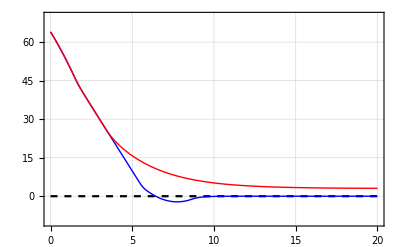

```mathematica
(*Plot of safety constraintvs time*)
Plot[{0, 
If[t ≤ domCLFCBFQP, hCLFCBFQP, Indeterminate],
If[t≤ domICCBFQP, hICCBFQP,Indeterminate]
},
 {t, 0, tmax},
 PlotRange->{-10, 70}, AxesOrigin->{0,0}, GridLines->Automatic, Frame->True ,PlotStyle->{{Dashed,Black} ,{Thick, Blue}, {Thick, Red}}]
```

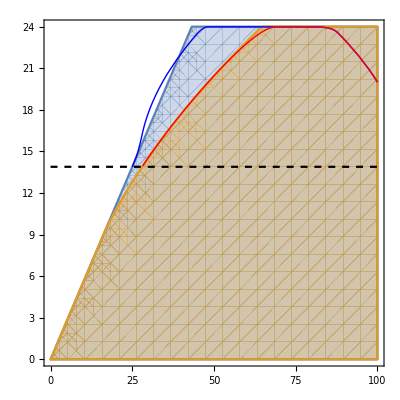

```mathematica
(*Plot of paths in state space*)
paths = ParametricPlot[ 
{
If[t≤ domCLFCBFQP,Evaluate[{y1[t], y2[t]}/.solCLFCBFQP], Indeterminate],
If[t≤ domICCBFQP,Evaluate[{y1[t], y2[t]}/.solICCBFQP], Indeterminate]
},
{t, 0, tmax},
 PlotRange->Full, PlotStyle->{{Thick, Blue}, {Thick, Red}}];
Show[regs, Plot[v0,{x1,0,100},PlotStyle->{Dashed, Black}],  paths]
```

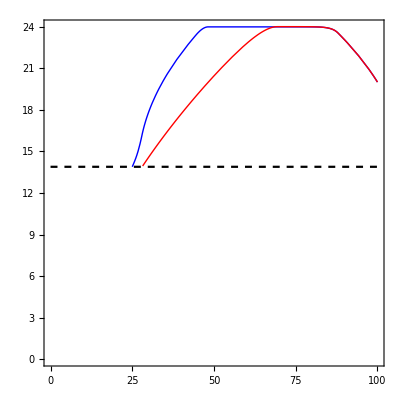

```mathematica
Show[RegionPlot[False, {x1,0,100},{x2,0,24}],Plot[v0,{x1,0,100},PlotStyle->{Dashed, Black}],  paths]
```

## Comparison to Optimal Viability Set

Now, lets try to determine the true unsafe regions, by simulating backwards in time, applying the maximum brakes:

```mathematica
x2crit = x2/.FindRoot[(f - g umax)[[2]]/(f - g umax)[[1]] ==1/1.8, {x2, 15}]
```

18.4988

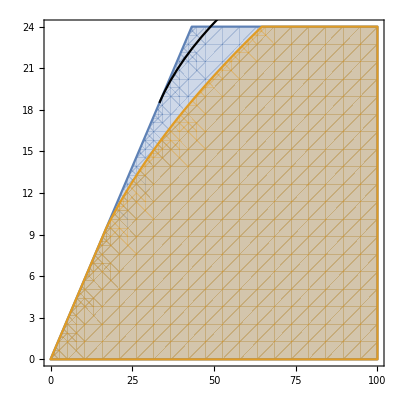

```mathematica
eqs = {y1'[t] == (f[[1]] + g[[1]] (-umax))/.{x1-> y1[t],x2-> y2[t]},
y2'[t] == (f[[2]] + g[[2]] (-umax))/.{x1-> y1[t],x2-> y2[t]},
y1[0] == 1.8*x2crit, y2[0] == x2crit}/.s-> 30;
tmax = 15;
sol = NDSolve[eqs, {y1, y2}, {t, -tmax,tmax}];
para = ParametricPlot[Evaluate[{y1[t], y2[t]}/.sol], {t, -tmax, 0}, PlotStyle->Black];
Show[regs, para]
```

Everything below the black line is the true viability kernel.

```mathematica
49 vs 64
```